# Chapter. Potential sweep methods

## Reversible reactions

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[NDSolve::"bdisc"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->80,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12], 
     Cell[TextData[{"Potential sweep methods"}], FontFamily->"Arial",FontSize->12],None}, {None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Laplace transform solution","Spherical diffusion","Numerical solution to the Volterra equation","Solution using NDSolve","Finite difference methods","Summary","Further reading"},#]&)]], 
FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[];
Symbolize[c^_];
Symbolize[Subscript[r, _]];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameLabel-> None,
FrameStyle->{Black,AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]}];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
FrameLabel->None,
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotStyle->{Black,AbsoluteThickness[.5]},
PlotLabel->None];
```

```mathematica
SetOptions[Plot3D,
AspectRatio-> 1,
AxesEdge->{{1,-1},{-1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
option1={
(*PlotRange:>{{0,init-switch}, {0, -0.5}},*)
AxesOrigin-> {0,0},
FrameTicks->{ticks1[0,30,5,5],ticks1[.6,-.6,-.2,5],ticks2[0,30,5,5],ticks2[.6,-.6,-.2,5]},
FrameLabel->{
Style["σt",FontFamily-> "Times New Roman",12,Italic,Plain],
Style["√πχ",FontFamily-> "Times New Roman",12,Plain],
None,
None}
};
```

```mathematica
option2={
PlotRange:>{{0,n}, {.4, -0.5}},
FrameTicks->{ticks1[0,250,50,5],ticks1[.6,-.6,-.2,5],ticks2[0,250,50,5],ticks2[.6,-.6,-.2,5]},
FrameLabel->{
Style["k",FontFamily-> "Times New Roman",2,Italic],
Style["√πχ",FontFamily-> "Times New Roman",12],
None,
None}
};
```

```mathematica
option3={
PlotRange-> {{0,20},{0,.5}},
FrameTicks->{ticks1[-30,30,5,5],ticks1[.6,-.6,-.2,5],ticks2[-30,30,5,5],ticks2[.6,-.6,-.2,5]},
FrameLabel->{
Style["σt",FontFamily-> "Times New Roman",12,Italic],
Style["√πχ",FontFamily-> "Times New Roman",12],
None,
None}
};
```

```mathematica
optionC={
AspectRatio->1/ GoldenRatio,
BaseStyle->Black,
FrameTicks-> {None,Automatic,None,None},
PlotStyle->{Dashed,AbsoluteThickness[1]}
};
```

```mathematica
optionD={
AspectRatio->1/GoldenRatio,
BaseStyle->Black,
FrameTicks-> None,
ImageSize->100,
PlotStyle->{Dashed,AbsoluteThickness[1]}
};
```

This for Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

```mathematica
Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i_[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;
(*Protect[InverseLaplaceTransform];*)
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In the preceding four chapters we introduced some methods to solve electrochemically related problems using finite difference methods. In the following chapters we apply those methods to simulate electrochemical problems beginning in this chapter with the simulation of reversible cyclic voltammograms using both analytical and numerical methods. We begin by showing how Mathematica can be used to apply Laplace transforms to obtain a solution to Fick’s second law with boundary conditions governed by cyclic voltammetry. We then solve the Volterra equation numerically and finally use fully explicit and implicit finite difference methods to simulate a reversible reaction by solving Fick’s second law directly. In Chapter 6 we extend these methods to quasi-reversible reactions.

## Chapter.Section Laplace transform solution

Cyclic voltammetry is probably the most commonly used voltammetric technique, although in practice these days most commercial equipment implements it as a cyclic staircase voltammogram (§8.3). The analytical solution can be obtained by using Laplace transforms. Under conditions of reversible electron transfer the equation describing the variation of current with potential is derived from the following equations.

O + ne ⇌ R

(∂c_O(x,t))/(∂t)=D_O(∂^2 c_O(x, t))/(∂x^2)

Assuming no R initially present the initial condition is

c_O(x, 0)=c_O^*
c_R(x, 0)=0

and the boundary condition

c_O(∞,t)=c_O^*
c_R(∞,t)=0

The solution begins by taking Laplace transforms of both sides of eqn (Chapter.EquationNumbered)

```mathematica
planar=LaplaceTransform[D[c[x,t],t]==𝒟*D[c[x,t],{x,2}],t,s]
```

-c[x,0]+s C[s][x]==𝒟 C[s]''[x]

The Laplace transform of c(x,t) with respect to t is expressed as a function of x, C[s][x]. DSolve may be used to find C[s][x] and the initial boundary condition, c[x,0]→c^✶, is inserted.

```mathematica
soln =DSolve[planar /.
 c[x,0] -> c^✶, C[s][x], x]//Simplify
```

{{C[s][x]→c^✶/s+ⅇ^((√s x)/(√𝒟)) C[1]+ⅇ^(-(√s x)/(√𝒟)) C[2]}}

The boundary condition at an infinite distance from the electrode surface is then set up

```mathematica
Simplify[soln/. x -> Infinity,{s>0,𝒟>0}]
```

{{C[s][∞]→c^✶/s+C[1] ∞}}

For the boundary condition in eqn (Chapter.EquationNumbered) to hold C[1] must equal zero:

```mathematica
soln=soln /. C[1]->0
```

{{C[s][x]→c^✶/s+ⅇ^(-(√s x)/(√𝒟)) C[2]}}

Re-writing this equation in traditional form gives

(c^-)_O(x, s)=c_O^*/s+Bexp[-(x(s/D_O))^(1/2)]

where B is a constant that is evaluated from the second boundary condition which is

(i(t))/(n F A)=D_O[(∂c_O(x, t))/(∂x)]_(x=0)=-D_R[(∂c_R(x, t))/(∂x)]_(x=0)

Transforming the boundary condition in eqn (Chapter.EquationNumbered) gives

```mathematica
LaplaceTransform[i_[t_],t_,s_]:=i[s];
boundary2=LaplaceTransform[i[t]/(n*F*A*𝒟)==D[c[x,t],{x,1}], t, s]
```

i[s]/(A F n 𝒟)==C[s]'[x]

Taking the derivative of eqn (Chapter.EquationNumbered) gives

```mathematica
soln2=D[soln⟦1⟧, x]
```

{C[s]'[x]→-(ⅇ^(-(√s x)/(√𝒟)) √s C[2])/(√𝒟)}

Therefore the derivative with respect to x at x=0 is

```mathematica
soln2=soln2⟦1,2⟧/.x-> 0
```

-(√s C[2])/(√𝒟)

This result can be inserted into the surface boundary condition to solve for C[2].

```mathematica
soln3=Solve[soln2==boundary2⟦1⟧,C[2]]
```

{{C[2]→-i[s]/(A F n √s √𝒟)}}

Therefore

B=-(i^-(s))/(n F (A(sD_O))^(1/2))

Substituting this equation for B into eqn (Chapter.EquationNumbered) gives

```mathematica
soln4=soln⟦1,1⟧ /.soln3⟦1,1⟧
```

C[s][x]→c^✶/s-(ⅇ^(-(√s x)/(√𝒟)) i[s])/(A F n √s √𝒟)

Re-written in traditional form this equation is

(c^-)_O(x,s)=c_O^*/s-(i^-(s))/(n F A (s D_O)^(1/2))exp(-(x(s/D_O))^(1/2))

At x=0 eqn (Chapter.EquationNumbered) becomes

```mathematica
soln4=soln⟦1,1⟧ /.{soln3⟦1,1⟧,x-> 0}
```

C[s][0]→c^✶/s-i[s]/(A F n √s √𝒟)

(c^-)_O(0,s)=c_O^*/s-(i^-(s))/(n F (A(s D_O))^(1/2))

which is of the form

(c^-)_O(0,s)=c_O^*/s-1/(n F A D_O^(1/2))f(s)*g(s)

where f(s)=i^-(s) and g(s)=s^(-1/2). Referring to §1.5.4 the reader will recognize eqn (Chapter.EquationNumbered) as being the Laplace transform of a convolution integral. The solution of eqn (Chapter.EquationNumbered) is therefore

```mathematica
soln5= InverseLaplaceTransform[soln4, s, t]⟦2⟧
```

c^✶-(∫_0^t i[τ]/(√(t-τ))ⅆτ)/(A F n √π √𝒟)

therefore

c_O(0,t)=c_O^*-1/(n F (A(π D_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

Similarly the concentration of R at x=0 is

c_R(0,t)=1/(n F (A(π D_R))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

By changing the integration variable from τ to τ=z/σ where σ=nFυ/RT eqn (Chapter.EquationNumbered) is rewritten as

c_O(0,t)=c_O^*-1/(n F (A(σ πD_O))^(1/2))∫_0^σt (i(z))/(σt-z)^(1/2)ⅆz

Under reversible conditions the ratio of O to R at the electrode surface at any potential is given by the Nernst equation.

(c_O(0,t))/(c_R(0,t))=exp((n F/R T)(E-E °'))=θ_c exp(-(n F/R T)υt)

where υ is the constant sweep rate and

θ_c=ex((n F/R T)(E_i-E °'))

with E_i being the initial potential. Substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into (Chapter.EquationNumbered) and assuming that no R is present in the bulk solution gives

1/(1+γ θ_c exp(-(n F/R T)υt))=1/(n F A (c_O^*(σπD_O))^(1/2))∫_0^σt (i(z))/(σt-z)^(1/2)ⅆz

where γ=(D_O/D_R)^(1/2). Equation (Chapter.EquationNumbered) can be simplified to

g(σt)=∫_0^σt (χ(z))/(σt-z)^(1/2)ⅆz

where

g(σt)=1/(1+γ θ_c exp(-σt))

and χ(σ t) is the dimensionless current defined as

χ(σt)=(i(σt))/(n F A (c_O^*(σπD_O))^(1/2))

Equation (Chapter.EquationNumbered) falls into a general category of equations known as a Volterra equations of the first kind. This type of Volterra equation has the general solution

χ(σt)=(g(0))/(π(σt))^(1/2)+1/π∫_0^σt 1/(σt-z)^(1/2)((dg(σt))/(d(σt)))_(σt=z)ⅆz

The integral in eqn (Chapter.EquationNumbered) has to be solved numerically. In order to avoid the singularity that exists at σ t=z integration by parts i.e. ∫u dv/dz ⅆz=u v-∫v du/dz ⅆz, is applied to the integral term in eqn (Chapter.EquationNumbered).

```mathematica
ClearAll[σt,z];
∫1/(√(σt-z))ⅆz
```

-2 √(-z+σt)

```mathematica
D[-2 √(σt-z),z]
```

1/(√(-z+σt))

By letting v=-2(σ t-z)^(1/2) and u=(dg(σ t))/(d(σ t)) eqn (Chapter.EquationNumbered) becomes

χ(σt)=(g(0))/(π(σt))^(1/2)-(2/π[(σt-z)^(1/2)((dg(σ t))/(d(σ t)))])_0^σt+2/π∫_0^σt (σt-z)^(1/2)d/dz((dg(σ t))/(d(σ t)))_(σt=z)ⅆz

We can use Mathematica to evaluate the terms contained within eqn (Chapter.EquationNumbered).

```mathematica
ClearAll[θ,γ,σt,g];

g[σt_]=1/(1+γ*θ*Exp[-σt]);
f[z_]:=-2/Pi*√(σt-z)*g'[z]
f[σt]-f[0]//Simplify
```

(2 γ θ √σt)/(π (1+γ θ)^2)

```mathematica
g'[z]
```

(ⅇ^-z γ θ)/((1+ⅇ^-z γ θ)^2)

We can simplify this expression further by noting that γθ=e^lnγθtherefore the derivative of g(z) becomes

```mathematica
res1=g'[z]/.{ γ-> Exp[ln[γ]],θ-> Exp[ln[θ]]}
```

ⅇ^(-z+ln[γ]+ln[θ])/((1+ⅇ^(-z+ln[γ]+ln[θ]))^2)

(d g)/dz=e^(ln γθ-z)/((1+e^(lnγθ-z))^2)

Alternatively this can be converted to a trigonometric expression using ExpToTrig

```mathematica
Simplify[ExpToTrig[res1]/.{ln->Log}]
```

1/4 Sech[1/2 (z-Log[γ]-Log[θ])]^2

Noting that Sech(x/2)=Sech(-x/2)

```mathematica
Sech[x/2]== Sech[-x/2]
```

True

dg/dz can be simplified to

(d g)/dz=1/4 Sech^2((ln γθ-z)/2)

The derivative of eqn (Chapter.EquationNumbered) is d^2 g/d z^2

```mathematica
D[1/4 Sech[1/2 (Log[γ*θ]-z)]^2,z]
```

1/4 Sech[1/2 (-z+Log[γ θ])]^2 Tanh[1/2 (-z+Log[γ θ])]

Therefore substituting this output back into eqn (Chapter.EquationNumbered) gives

χ(σt)=1/((π(σt))^(1/2)(1+γ θ_c))+(2γ (θ_c(σt))^(1/2))/(π(1+γ θ_c))^2+1/(2π)∫_0^σt (σt-z)^(1/2)tanh[(lnγ θ_c-z)/2]/(cosh^2[(lnγ θ_c-z)/2])ⅆz

The dimensionless current is traditionally plotted as √π χ(σt) rather than χ(σt) and since θ_c≫1, eqn (Chapter.EquationNumbered) reduces to

π^(1/2)χ(σ t)=1/(2 π^(1/2))∫_0^σt (σt-z)^(1/2)tanh[(ln γ θ_c-z)/2]/(cosh^2[(ln γ θ_c-z)/2])ⅆz	for t>0

A linear sweep voltammogram is readily simulated from eqn (Chapter.EquationNumbered) using the NIntegrate function to perform the numerical integration.

In the simulation described below we will assume that D_O=D_R, therefore γ =1.

```mathematica
ClearAll[init,switch,cv,incr];

init=10.(*=lnθ*);
switch=-10.;
incr=0.05;

cv=Table[{σt,-1/(2*Sqrt[Pi])*NIntegrate[Sqrt[σt-z]*Tanh[(init-z)/2]/(Cosh[(init-z)/2]^2),{z,0,σt}]},{σt,0.,init-switch,incr}];
```

The result of the calculation is shown in fig. 6.FigureCaption.

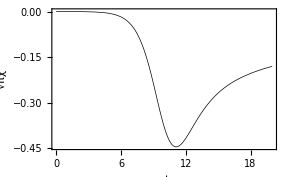

```mathematica
ListPlot[cv,option1]
```

Fig. Chapter.FigureCaption  Simulated linear sweep voltammogram for a reversible one electron reaction

The baseline for the forward simulated sweep is of course zero current. On the reverse sweep the baseline is the current that would have been observed had no reversing of the sweep direction taken place. To simulate the entire voltammogram we therefore have to simulate the cathodic current from 20<σt<40 and add this to the simulated anodic current. For the anodic sweep some minor changes to eqn (Chapter.EquationNumbered) need to be made. Since the sweep is in the reverse direction the derivation following the same steps as above leads to +z rather than -z as the argument for the hyperbolic functions. The term θ which was a function of the initial potential now also becomes a function of the potential range covered at the time, t_s, that the sweep is reversed.

θ_a=exp[(n F/R T)(E_i-2υ t_s-E°')]

After making these changes to the anodic sweep the dimensionless current, relative to the baseline, is given by

π^(1/2)χ(σt)=1/(2 π^(1/2))∫_0^σt (σt-z)^(1/2)tanh[(ln γ θ_a+z)/2]/(cosh^2[(ln γ θ_a+z)/2])ⅆz	for t>t_s

and the absolute anodic dimensionless current is

π^(1/2)χ(σt)=1/(2 π^(1/2))∫_0^σt (σt-z)^(1/2)tanh[(ln γ θ_c-z)/2]/(cosh^2[(ln γ θ_c-z)/2])ⅆz+1/(2 π^(1/2))∫_0^σt (σt-z)^(1/2)tanh[(ln γ θ_a+z)/2]/(cosh^2[(ln γ θ_a+z)/2])ⅆz 	for t> t_s

The dimensionless current is plotted against the dimensionless time, σ t, as shown in Fig. Chapter.FigureCaption. note

(see accompanying notebook CVNumerical.nb.)

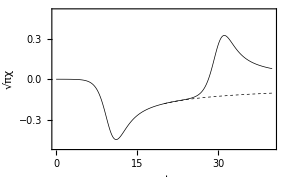

Fig. Chapter.FigureCaption  Simulated cyclic voltammogram for a reversible one electron reaction.

Changing the x axis to reflect dimensionless potential rather than dimensionless time is readily accomplished. The result is shown in Fig. 6.FigureCaption.

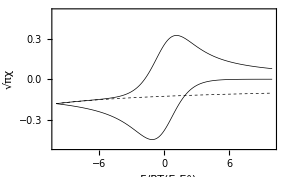

Fig. Chapter.FigureCaption  Simulated cyclic voltammogram for a reversible one electron reaction.

## Chapter.Section Spherical diffusion

Chapter.Section.Subsection Diffusion to spherical electrodes

For diffusion to a spherical electrode Fick’s second law has the form

(∂c_O(r,t))/(∂t)=D_O(∂^2 c_O(r,t))/(∂r^2)+D_O 2/r(∂c_O(r,t))/(∂r)

with the initial condition

c_O(r,0)=c_O^*
c_R(r,0)=0	for r > r_0

and the boundary conditions

c_O(∞,t)=c_O^*
c_R(∞,t)=0

Under reversible conditions the concentrations at the surface are

c_O(r_0,t)=(c_O^*γ θ_c exp(-σt))/(1+γ θ_c exp(-σt))

Making the transformation described in §1.4.4 and assuming that no R is initially present,

u(r,t)=r c_O^*-r c_O(r,t)

therefore we have

(∂u(r,t))/(∂t)=-D_O(∂^2 u(r,t))/(∂r^2)

with the initial condition

u(r,0)=0	for r > r_0

and the boundary conditions

u(∞,t)=0

Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

u(r_0, t)=(r_0 c_O^*)/(1+γ θ_c exp(-σt))

Next we take the Laplace transform of eqn (Chapter.EquationNumbered).

```mathematica
ClearAll[r,t,u,v,c,sphericalU];

sphericalU=LaplaceTransform[D[u[r,t],t]==𝒟*D[u[r,t],{r,2}],t,s]
```

s LaplaceTransform[u[r,t],t,s]-u[r,0]==𝒟 U[s]''[r]

The Laplace transform of u(r, t) with respect to t is expressed as a function of r, U[s][r].

```mathematica
LaplaceTransform[u[r_, t_], t_, s_] := U[s][r];
sphericalU
```

SetDelayed::write: Tag LaplaceTransform in LaplaceTransform[u[r_,t_],t_,s_] is Protected.

s LaplaceTransform[u[r,t],t,s]-u[r,0]==𝒟 U[s]''[r]

DSolve may be used to find U[s][r] and the initial boundary condition, u[r,0] → 0, is inserted.

```mathematica
solnU =DSolve[sphericalU /.
 u[r,0] ->0, U[s][r], r]//Simplify
```

{{U[s][r]→C[1]+r C[2]+(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r}}

```mathematica
Simplify[solnU/. r -> Infinity,{s>0,𝒟>0}]
```

{{U[s][∞]→C[1]+C[2] ∞+(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1∞}}

For the boundary condition in eqn (Chapter.EquationNumbered) to hold C[1] must equal zero:

```mathematica
solnU=solnU /. C[1]-> 0
```

{{U[s][r]→r C[2]+(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r}}

Rewriting u^-(r, s) in traditional form gives

u^-(r,s)=Bexp(-(r(s/D_O))^(1/2))

B can be evaluated from the boundary at r=r_0. From eqn (Chapter.EquationNumbered) we have note

```mathematica
tempU=solnU/.r-> Subscript[r, o]
```

{{U[s][r_o]→r_o C[2]+(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r_o}}

```mathematica
temp2U=Solve[tempU⟦1,1,2⟧==tempU⟦1,1,1⟧,C[2]]
```

{{C[2]→(-(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r_o+U[s][r_o])/r_o}}

Therefore

B=u^-(r_0,s)exp((r_0(s/D_O))^(1/2))

Substituting this into the previous result gives

```mathematica
temp3=solnU/.C[2]-> temp2U⟦1,1,2⟧//FullSimplify
```

{{U[s][r]→(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r+(r (-(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r_o+U[s][r_o]))/r_o}}

u^-(r,s)=u^-(r_0,s)exp((r_0-r)(s/D_O)^(1/2))

Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) we see that

u^-(r,s)=r_0 c_O^*g^-(s)exp((r_0-r)(s/D_O)^(1/2))

where

g( t)=1/(1+γ θ_c exp(-σt))

From eqn (Chapter.EquationNumbered) its follows that

(∂c_O(r,t))/(∂r)=-(u(r,t))/r^2+1/r(∂u(r,t))/(∂r)

and with the current defined as

(i(t))/(n F A)=(D_O((∂c_O(r,t))/(∂r)))_(r=r_0)

eqn (Chapter.EquationNumbered) becomes

(i(t))/(n F A)=-D_O/r_0^2u(r_0,t)+D_O/r_0((∂u(r,t))/(∂r))_(r=r_0)

At r = r_0 eqn (Chapter.EquationNumbered) becomes

u^-(r_0,s)=r_0 c_O^*g^-(s)

Therefore

u(r_0,t)=r_0 c_O^*g(t)

Taking the derivative of eqn (Chapter.EquationNumbered) at r = r_0 gives

```mathematica
D[temp3,r]/.{U[s][Subscript[r, o]]-> G[s]*SuperStar[c]*Subscript[r, o],r-> Subscript[r, o]}
```

{{U[s]'[r_o]→(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1r_o+(c^* r_o G[s]-(s LaplaceTransform[u[K[1],t],t,s])/𝒟K[1]1K[2]K[2]1r_o)/r_o}}

((∂u^-(r,s))/(∂r))_(r=r_0)=-r_0 c_O^*g^-(s)(s/D_O)^(1/2)

The Laplace transform of the derivative of g with respect to t is

```mathematica
ClearAll[g];

LaplaceTransform[D[g[t],t], t, s]
```

g'[s]

ℒ{(dg(t))/(d t)}=sg^-(s)-g(0)

Since at t=0, θ_c≫ 1, g(0)→0 therefore

g^-(s)=1/s ℒ{(dg(t))/(d t)}

The inverse Laplace transform of s^(-1/2) is

```mathematica
InverseLaplaceTransform[1/s^(1/2),s,t]
```

1/(√π √t)

Equation (Chapter.EquationNumbered) can be written as the product of two Laplace transformed functions:

((∂u^-(r,s))/(∂r))_(r=r_0)=-(r_0 c_O^*)/D_O^(1/2)ℒ{1/(πt)^(1/2)}ℒ{(dg(t))/dt}

Substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) we get

(i(t))/(n F A)=-(c_O^*D_O g(t))/r_0-c_O^*D_O^(1/2)ℒ^-1(ℒ{1/(πt)^(1/2)}ℒ{(dg(t))/dt})

The second part of this equation contains the inverse Laplace transform of two Laplace transformed functions therefore the inverse transform is a convolution integral.

(i(t))/(n F A)=-(c_O^*D_O g(t))/r_0- c_O^* (D_O/π)^(1/2)∫_0^t 1/(t-τ)^(1/2)((dg(t))/dt)_(t=τ)ⅆτ

As shown above the integral can be transformed by applying integration by parts. The result is:

-(2[(t-τ)^(1/2)((dg(t))/(d t))])_0^t+2∫_0^t (t-τ)^(1/2)d/dτ((dg(t))/dt)_(t=τ)ⅆτ

The large value of θ_c, θ_c≫1, causes the first part of eqn (Chapter.EquationNumbered) to be approximately zero. Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives

(i(t))/(n F A)=-(c_O^*D_O g(t))/r_0-2 c_O^* (D_O/π)^(1/2)∫_0^t (t-τ)^(1/2)d/dτ((dg(t))/dt)_(t=τ)ⅆτ

Changing the integration variable from τ to τ=z/σ where σ=n F υ/R T gives

(i(σt))/(n F A)=-(c_O^*D_O g(σt))/r_0- c_O^* (σπD_O)^(1/2)2/π∫_0^σt (σt-z)^(1/2)d/dz((dg(σ t))/(d(σt)))_(σ t=z)ⅆz

For a planar electrode r_0→∞ so that for a planar electrode the first term on the left hand side of eqn (Chapter.EquationNumbered) would be zero. Thus the equation would reduce to

χ(σt)=(i(σt))/(n F A c_O^* (σπD_O)^(1/2))=-2/π∫_0^σt (σt-z)^(1/2)d/dz((dg(σ t))/(d(σt)))_(σ t=z)ⅆz

which is the equation derived in the previous section. We therefore see that at spherical electrodes the current is equal to the planar current plus an additional spherical term. In dimensionless for the current is

(i(σt))/(n F A c_O^* (σπD_O)^(1/2))=-(g(σt))/r_0(D_O/σπ)^(1/2)-2/π∫_0^σt (σt-z)^(1/2)d/dz((dg(σ t))/(d(σ t)))_(σ t=z)ⅆz

The shape of the resulting voltammogram will depend on the radius of the electrode and the sweep rate.

### Chapter.Section.Subsection Edge effects

It should be remembered that semi-infinite planar diffusion models in electrochemistry assume that the electrode is an infinite plane. In reality the electrode is of finite size and usually embedded into some inert material. Diffusion to its edges is non-planar (Fig 6.FigureCaption) and contributes differently to the magnitude of the current.

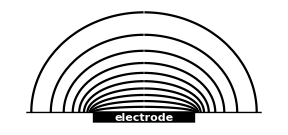

```mathematica
Clear[z,r,radialData,electrode];

z[θ_,Γ_]:= (1-θ^2)^(1/2)/Cos[Pi*Γ/2];
r[θ_,Γ_]:= θ*Tan[Pi*Γ/2];

radialData[Γ_] := {First[ParametricPlot[{{-z[θ,Γ],r[θ,Γ]},{z[θ,Γ],r[θ,Γ]}},{θ, 0, 3},
PlotRange->{{-2.3,2.3},Automatic},
PlotRangePadding->{{0,0},{0.25,0}},
PlotStyle-> {Black,Black}
]]}

electrode=Style["electrode",FontFamily->"Arial",White,Bold,FontTracking-> "Extended"];

Graphics[{
radialData /@ Range[0,.7, 0.07],
Rectangle[{-1.0,-.2},{1,0}],
Text[electrode,{0,-.1}],
Line[{{-2.3,0},{2.3,0}}]
}]

SelectionMove[EvaluationNotebook[],Previous,Cell];
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell];
```

Fig. Chapter.FigureCaption  Diffusion to the edge of an electrode is radial rather than planar.

As a first approximation a spherical correction can be used to estimate the total current resulting from both planar and radial diffusion. By using eqn (Chapter.EquationNumbered) to calculate the dimensionless current π^(1/2)χ_sp(σt) to a planar electrode of radius r_0, one can get a feel for the effect that radial diffusion might have on the voltammogram. Equation (Chapter.EquationNumbered) can be rewritten as

π^(1/2)χ_sp(σt)=(g(σt))/r_0(D_O/σ)^(1/2)+π^(1/2)χ_pl(σt)

where π^(1/2)χ_pl(σt) is the planar dimensionless current. For small electrode radii and slow sweep rates radial diffusion will become more significant. Some examples are shown in Fig 6.FigureCaption. note

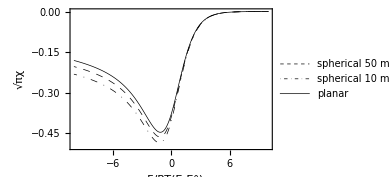

Fig. Chapter.FigureCaption  Linear sweep voltammograms simulated using eqn (Chapter.EquationNumbered). Bottom two voltammograms; r_0=1.0 mm and υ=10 mV · s^-1 (bottom) and 50 mV · s^-1(middle). Top voltammogram has no spherical component.

## Chapter.Section Numerical solution to the Volterra equation

Equation (EquationNumbered) should look familiar from §4.6. It has the form

g(σt)=∫_0^σt K(t,z)f(z)ⅆz

where

g(σt)=1/(1+γ θ_c exp(-σt))

and the kernel K(t,z) is

K(t,z)=(σt-z)^(-1/2)

For γ=1 and large θ_c, say θ_c=10, the problem is the same as the example problem solved in §4.6 which demonstrated the numerical solution of the Volterra equation of the first kind.

## Chapter.Section Solution using NDSolve

Reversible linear sweep voltammograms can be simulated using the function NDSolve although problems may arise due to the discontinuity in the boundary conditions. The problem is set up by entering the partial differential equation and the boundary conditions. Below the concentration profile during a linear sweep voltammogram is simulated using an expanding grid:

```mathematica
ClearAll[xList,tList,σ,result,c,x,t];

xList=Join[{x,0},Table[1.05^-j,{j,100,0,-1}]];
σ=100;
tList=Join[{t},Table[.2*j/σ,{j,0,100}]];

result=c/.First[
NDSolve[{D[c[x,t],t]==D[c[x,t],{x,2}],c[x,0]==1.,c[0,t]==If[t>0,Exp[10.-σ*t]/(1+Exp[10.-σ*t]),1.],c[1,t]==1.},c,
xList,tList,MaxSteps-> 4000,MaxStepSize->1/5000]];
```

```mathematica
Plot3D[result[x,t],{x,0.,1.},{t,0.,20./σ},ViewPoint-> {-2.36, 3.58, 2.00}]
```

-Graphics3D-

Fig. Chapter.FigureCaption  NDSolve solution, using an expanding space grid, of the concentration profile for a reversible linear sweep voltammogram.

The dimensionless current is obtained by taking the derivative of the result at x=0. Plotting the current by executing either of the functions below is inefficient since the derivative at x=0 must be re-evaluated at each time increment.

```mathematica
Plot[(D[result[x,t],x]/.x->0)/Sqrt[σ],{t,0.,20./σ}];//Timing

Plot[Evaluate[D[result[x,t],x]/.x->0]/Sqrt[σ],{t,0.,20./σ}];//Timing
```

{0.116881,Null}

{0.100298,Null}

It is more efficient to evaluate the derivative at x=0 once and then plot this over a range of values of t. Note that the function is defined using Set (i.e. = ) rather than SetDelayed (i.e. :=). Had set delayed been used the function would have been re-evaluated at each time step and no efficiency gains would have been made. The plot below shows the dimensionless current.

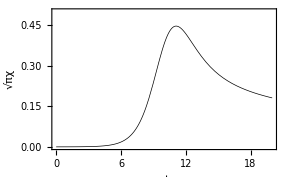

```mathematica
lsv[t_]=(D[result[x,t],x]/.x-> 0);

Plot[lsv[t/σ]/Sqrt[σ],{t,0.,20.},Evaluate[option3]]
```

Fig. Chapter.FigureCaption  NDSolve solution of the current for a reversible linear sweep voltammogram.

## Chapter.Section Finite difference methods

Chapter.Section.Subsection Explicit methods

To simulate a reversible cyclic voltammogram using either explicit or implicit finite difference methods the surface boundary condition differs from that described in the introduction to finite difference methods in Chapter 2. Two adjustments to the procedures described in §2.3 need to be made to accommodate the surface boundary condition for cyclic voltammetry. For the reversible reaction the ratio of O to R is given by eqn (Chapter.EquationNumbered) that can re-written as

(c_O(0,t))/(c_R(0,t))=exp((n F/R T)(E-E°')_)=ξ

therefore

c_O(0,t)=ξ/(1+ξ)

and

c_R(0,t)=1/(1+ξ)

Below we’ll examine some of the code taken from the notebook ExplicitCVRev.nb.

If we want to plot changes in the concentration profiles in the diffusion layer the grid now has to contain information on the dimensionless concentrations of both O and R that initially have concentrations of 1. and 0. respectively.

The value of ξ will change incrementally with k

ξ(k)=exp((n F/R T)(E_i-E °')-_ τ(k-1))

where τ is the dimensionless incremental change in potential and E_i is the initial potential. The code fragment below, from the procedural explicit method, shows how to include the boundary concentrations of O (c⟦j,k,1⟧) and R (c⟦j,k,2⟧).

For[k=2,k≤(n+1)/2,k++,
ξ=Exp[upperLimit-((k-1)*τ)];
For[j=2,j≤m-1,j++,
c⟦j,k⟧=𝔻*c⟦j-1,k-1⟧+(1.-2.*𝔻)*c⟦j,k-1⟧+𝔻*c⟦j+1,k-1⟧;
c⟦1,k⟧=ξ/(1.+ξ)
]
]

You may have noticed that the loop continues until k ≤ (n + 1)/2 rather than k ≤ n. This section of code simulates the cathodic sweep. For the anodic sweep a second loop is added and ξ redefined with the variable region being equal to twice the dimensionless sweep range.

For[k=(n+3)/2,k≤n,k++,
ξ=Exp[upperLimit-region+((k-1)*τ)];
For[j=2,j≤m-1,j++,
c⟦j,k⟧=𝔻*c⟦j-1,k-1⟧+(1.-2.*𝔻)*c⟦j,k-1⟧+𝔻*c⟦j+1,k-1⟧;
c⟦1,k⟧=ξ/(1.+ξ)
]
]

To calculate the dimensionless current we begin with the equation relating the current to the concentration flux:

i(t)=-n F A (D_O((∂c_O(x,t))/(∂x)))_(x=0)

Diving both sides by n F A c_O^* (σ D_O)^(1/2) gives:

π^(1/2)χ(σt)=(i(t))/(n F A c_O^* (σ D_O)^(1/2))=-( D_O/σ)^(1/2)((∂c_O(x,t))/(∂x))_(x=0)

After differencing the partial derivative we have

π^(1/2)χ(σt)=( D_O/σ)^(1/2)(3 c_1^k-4 c_2^k+c_3^k)/(2Δ x)

Substituting Δ x=(D Δ t/D)^(1/2) and Δ t=t_n/(n-1) into this equation gives the dimensionless current:

π^(1/2)χ(σt)=( (D(n-1))/t_n)^(1/2)(3 c_1^k-4 c_2^k+c_3^k)/2

where t is the dimensionless time

t_n=σ t_n

The formula for calculating the dimensionless current is therefore:

cv1=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*√(𝔻*(n-1))/√(𝕥*4))&,c];

There are several ways in which the problem can be tackled functionally. The most obvious way of writing a method analogous to the procedural method is to use the function ListCorrelate.

solveCV[list_List,y_Integer]:=Module[{},Flatten[{ξ[y]/(1.+ξ[y]),ListCorrelate[{𝔻,(1.- 2.*𝔻),𝔻},list],1.}]];

Once the boundary condition has been established the new concentration values are calculated with the function ListCorrelate as described in §2.5. The boundary conditions are added with the command Flatten[{boundary condition, list, boundary condition}]. Each list that is used as input into ListCorrelate contains pairs of O and R eg. {{1., 0.}, {1., 0.} …}. ListCorrelate can handle this type of list as an input as long as the kernel is a list with the same dimensions, i.e. {{numbers},{numbers},…} therefore the ListCorrelate kernel for this problem is {{𝔻},{1.-2.*𝔻},{𝔻}} rather than {𝔻,1.-2.*𝔻,𝔻}.

The function explicitCV, shown below, solveCV is applied repeatedly beginning with the initial concentrations of O and R, that are set by the initial potential. After (n + 1)/2 nested loops ξ is redefined solveCV is applied repeatedly beginning with the last row of concentrations returned from the set of nested loops. The output from the two nested loops corresponding to the forward and backward sweeps is then joined to create one list of data for the entire cyclic voltammogram.

```mathematica
Clear[explicitCV];

explicitCV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_}]:=Module[{solveCV,for,back,row,ξ,range,τ},
range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1)//N (*calculation of the incremental time/potential step*);
row=ConstantArray[1.,{m}];

solveCV[list_List,y_Integer]:=Module[{},Flatten[{ξ[y]/(1.+ξ[y]),ListCorrelate[{d,(1.- 2.*d),d},list],1.}]];
ξ[y_]:=Exp[upperLimit-((y-1)*τ)];
for=FoldList[solveCV,row,Range[1,(n+1)/2]];

Clear[ξ];
ξ[y_]:=Exp[upperLimit-range+((y-1)*τ)];
back=FoldList[solveCV,Last[for],Range[(n+3)/2,n]];

Join[Drop[for,1],Drop[back,1]]
]/;OddQ[n]
```

Because the nested loop is applied a given number of times we require that (n + 1)/2 is an integer. In other words this method has been set up to operate for odd values of n. At the end of the explicitSolve function a statement, /;OddQ[n], is included to get Mathematica to check that n is an odd number. If the input n is not an odd number Mathematica will not try to evaluate the result thereby avoiding a lot of error messages. /; is short form for Condition. In this case the pattern is n_ and the condition is OddQ[n], i.e. is n an odd number? If an even numbered n is entered no evaluation occurs.

```mathematica
explicitCV[8, 6]
```

explicitCV[8,6]

After assigning values to the variables the voltammogram can be simulated.

```mathematica
ClearAll[lowerLimit,upperLimit,𝕥,n,𝔻,m,τ];

lowerLimit=-8.(*limit = f×(E-E^o)*);
upperLimit=8.(*limit = f×(E-E^o)*);
𝕥=2*(upperLimit+Abs[lowerLimit]);
n=201;
𝔻=0.35;
m=1+Ceiling[6*√(𝔻*(n-1))];
τ=𝕥/(n-1)//N (*calculation of the incremental time/potential step*);
```

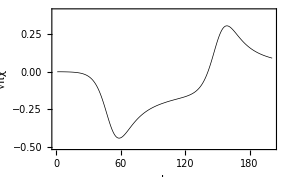

```mathematica
c=explicitCV[m,n,𝔻,{lowerLimit,upperLimit}];

cv1=Map[((3.*#⟦1⟧-4.*#⟦2⟧+#⟦3⟧)*√(𝔻*(n-1))/√(𝕥*4.))&,c];

plot1=ListPlot[cv1,option2]
```

Fig. Chapter.FigureCaption  Simulated reversible cyclic voltammogram.

Because we have been calculating concentration gradients of both O and R at each time increment without any additional effort the data can be used to create a movie of the changing concentration profiles. Each frame of the movie will be a plot of the concentration profile of the oxidant and reductant (one minus oxidant) at a given time increment. The plots are constructed from a list of calculated concentration values and a second list of one minus the calculated concentration values. The animation is made by wrapping Animate around the ListPlot function and determining how many frames you want in the animation. Below there are n time increments but only every fifth increment is plotted.

```mathematica
DynamicModule[{c=c,opts=optionC},
Animate[ListPlot[{c⟦j,All⟧,1.-#&/@c⟦j,All⟧},optionC], {j, 1,n, 5},AnimationRepetitions->1]
]
```

Alternatively some sample frames can be taken and shown in a graphics array. Here every twentieth frame is saved and plotted using GraphicsArray.

```mathematica
Clear[frames];
frames=Table[ListPlot[{c⟦j,All⟧,(1.-#1&)/@c⟦j,All⟧},optionD],{j,1,n,20}];
```

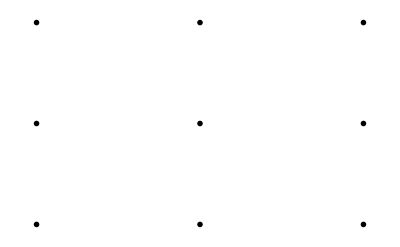

```mathematica
GraphicsGrid[Partition[frames,3]]
```

Fig. Chapter.FigureCaption  Typical concentration profiles during a cyclic voltammogram.

### Chapter.Section.Subsection Implicit Methods

Beginning with the series of equations for the concentrations at the jth increment

(1+2D)c_2^(k+1)-D c_3^(k+1)=c_2^k+D c_1^(k+1)
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-2)^(k+1)+(1+2D)c_(m-1)^(k+1)=c_(m-1)^k+D c_m^(k+1)

we see that the diagonals will be the same as those for the implicit method outlined in §2.6. Since the boundary values are known and given by eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) the only change to the implicit method described in §2.6 is to alter the boundary values as demonstrated in the code fragment below.

ξ[y_]:=Exp[upperLimit-((y-1)*τ)];

solveNext[list_List,j_Integer]:=Module[{b},
b=list⟦2;;-2⟧;
b⟦1⟧+=d*ξ[j]/(1.+ξ[j]);
b[[-1]]=b[[-1]]+d;
Flatten[{ξ[j]/(1.+ξ[j]),LinearSolve[mat,b],1.}]];

SolveNext is no longer a pure function and now takes two arguments. To facilitate its use FoldList replaces NestList as the function that calculates each incremental step. A full implicit solution is given in the notebook implicitCVRev.nb.

Clear[implicitSolveCV];

implicitSolveCV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_}]:=Module[{x,y,z,len,mat,initial,range,ξ,τ,solveNext},

(* added for dealing with cyclic voltammetry *)
range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);
ξ[k_]:=If[k>(n+1)/2,Exp[(upperLimit-range+(τ*(k-1)))],Exp[(upperLimit-(τ*(k-1)))]];
(*  ------- *)

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]→x,Band[{1,1}]→y,Band[{1,2}]→z},len];
initial=ConstantArray[1.,{m}];
solveNext[list_List,j_Integer]:=Module[{b},
b=list⟦2;;-2⟧;
b⟦1⟧+=d*ξ[j]/(1.+ξ[j]);
b[[-1]]=b[[-1]]+d;
Flatten[{ξ[j]/(1.+ξ[j]),LinearSolve[mat,b],1.}]];

FoldList[solveNext,initial,Range[2,n]]
]

## Chapter.Section Summary

In this chapter we have used the analytical methods outlined in Chapter 2 to develop a symbolic solution to the diffusion equation. The result could be solved numerically using the numerical solver in Mathematica. We also demonstrated how to simulate reversible cyclic voltammograms using finite difference methods. In the next chapter we extend both the analytical and numerical approach to the voltammetry of quasi-reversible reactions.

## Further reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Nicholson, R. S. and Shain, I. (1964). Analytical Chemistry, 36, 704-23.
Nicholson, R. S. and Olmstead, M. L. (1972). Numerical Solution of Integral Equations. In Electrochemistry; Calculations, Simulations, and Instrumentation, (eds. J. S. Mattson, H. B. Mark jnr., and H. C. MacDonald jnr.), pp. 119-38. Marcel Dekker, New York.
Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Cambridge University Press, New York.